## CMT equations

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={g0>0,  g0∈Reals,ωp1∈Reals,ωp2∈Reals,d1∈Reals,t∈Reals, τ∈Reals,μ∈Integers,κ[-1]∈Reals,κ[-1]>0, κ[0]∈Reals,κ[0]>0,κ[1]∈Reals,κ[1]>0,ω[-1]∈Reals,ω[-1]>0, ω[0]∈Reals,ω[0]>0,ω[1]∈Reals,ω[1]>0,  Δ∈Reals,  Δp∈Reals}
```

{g0>0,g0∈ℝ,ωp1∈ℝ,ωp2∈ℝ,d1∈ℝ,t∈ℝ,τ∈ℝ,μ∈ℤ,κ[-1]∈ℝ,κ[-1]>0,κ[0]∈ℝ,κ[0]>0,κ[1]∈ℝ,κ[1]>0,ω[-1]∈ℝ,ω[-1]>0,ω[0]∈ℝ,ω[0]>0,ω[1]∈ℝ,ω[1]>0,Δ∈ℝ,Δp∈ℝ}

```mathematica
validTriads[μ_]:=Select[Tuples[{-1,0, 1},3],(#[[1]]-#[[2]]+#[[3]]==μ)&]
(*Do[Print["μ = ",μ," → ",validTriads[μ]],{μ,{-1,0, 1}}];*)
```

```mathematica
eq[μ_]:=D[A[μ][t],t]==-(κ[μ]/2) A[μ][t]+
Sqrt[κe[μ]] Sn1*Exp[-I (ωp1-ω[μ]) t] KroneckerDelta[μ,-1]+
Sqrt[κe[μ]] S1* Exp[-I (ωp2-ω[μ]) t] KroneckerDelta[μ,1]+
I g0 Sum[With[{α=triad[[1]],β=triad[[2]],γ=triad[[3]]},
f[μ,α,β,γ]A[α][t]  Conjugate[A[β][t]] A[γ][t] Exp[-I (ω[α]-ω[β]+ω[γ]-ω[μ]) t]
],
{triad,validTriads[μ]}
];
eqsystem = Table[eq[μ],{μ,{-1,0, 1}}]
```

{A[-1]'[t]==ⅇ^(-ⅈ t (ωp1-ω[-1])) Sn1 √κe[-1]-1/2 κ[-1] A[-1][t]+ⅈ g0 (Conjugate[A[-1][t]] f[-1,-1,-1,-1] (A[-1][t])^2+Conjugate[A[0][t]] f[-1,-1,0,0] A[-1][t] A[0][t]+Conjugate[A[0][t]] f[-1,0,0,-1] A[-1][t] A[0][t]+ⅇ^(-ⅈ t (-ω[-1]+2 ω[0]-ω[1])) Conjugate[A[1][t]] f[-1,0,1,0] (A[0][t])^2+Conjugate[A[1][t]] f[-1,-1,1,1] A[-1][t] A[1][t]+Conjugate[A[1][t]] f[-1,1,1,-1] A[-1][t] A[1][t]),A[0]'[t]==-1/2 κ[0] A[0][t]+ⅈ g0 (Conjugate[A[-1][t]] f[0,-1,-1,0] A[-1][t] A[0][t]+Conjugate[A[-1][t]] f[0,0,-1,-1] A[-1][t] A[0][t]+Conjugate[A[0][t]] f[0,0,0,0] (A[0][t])^2+ⅇ^(-ⅈ t (ω[-1]-2 ω[0]+ω[1])) Conjugate[A[0][t]] f[0,-1,0,1] A[-1][t] A[1][t]+ⅇ^(-ⅈ t (ω[-1]-2 ω[0]+ω[1])) Conjugate[A[0][t]] f[0,1,0,-1] A[-1][t] A[1][t]+Conjugate[A[1][t]] f[0,0,1,1] A[0][t] A[1][t]+Conjugate[A[1][t]] f[0,1,1,0] A[0][t] A[1][t]),A[1]'[t]==ⅇ^(-ⅈ t (ωp2-ω[1])) S1 √κe[1]-1/2 κ[1] A[1][t]+ⅈ g0 (ⅇ^(-ⅈ t (-ω[-1]+2 ω[0]-ω[1])) Conjugate[A[-1][t]] f[1,0,-1,0] (A[0][t])^2+Conjugate[A[-1][t]] f[1,-1,-1,1] A[-1][t] A[1][t]+Conjugate[A[-1][t]] f[1,1,-1,-1] A[-1][t] A[1][t]+Conjugate[A[0][t]] f[1,0,0,1] A[0][t] A[1][t]+Conjugate[A[0][t]] f[1,1,0,0] A[0][t] A[1][t]+Conjugate[A[1][t]] f[1,1,1,1] (A[1][t])^2)}

```mathematica
A[μ_][t_]:=Sqrt[κ[0]/(2 g0)] a[μ][t] Exp[I (ω[μ]-ω[0]-μ*d1) t]
expr = eqsystem//Simplify;
```

```mathematica
expr = expr/. t->(2 τ)/κ[0];
```

```mathematica
rulesTime={ a[n_][(2 τ)/κ[0]]->a[n][τ],Derivative[1][a[n_]][(2 τ)/κ[0]]->(κ[0]/2) Derivative[1][a[n]][τ]};
expr= expr/.rulesTime//Simplify;
```

```mathematica
expr//MatrixForm
```

(ⅈ √2 ⅇ^((2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) √(κ[0]/g0) (-Conjugate[a[-1][τ]] f[-1,-1,-1,-1] κ[0] (a[-1][τ])^2-Conjugate[a[1][τ]] f[-1,0,1,0] κ[0] (a[0][τ])^2+a[-1][τ] (2 d1-ⅈ κ[-1]+2 ω[-1]-2 ω[0]-Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]-Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ])-ⅈ κ[0] a[-1]'[τ])==4 Sn1 √κe[-1]
-ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])+ⅈ a[0]'[τ])==0
4 ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) S1 √κe[1]+ⅈ √2 √(κ[0]/g0) (2 d1+ⅈ κ[1]+2 ω[0]-2 ω[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ]+ⅈ √2 g0 Conjugate[a[1][τ]] f[1,1,1,1] (κ[0]/g0)^(3/2) (a[1][τ])^2+ⅈ √2 g0 Conjugate[a[-1][τ]] (κ[0]/g0)^(3/2) (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])==√2 g0 (κ[0]/g0)^(3/2) a[1]'[τ])

```mathematica
(*Isolando o termo da derivada*)
expr = Solve[expr,{Derivative[1][a[-1]][τ],Derivative[1][a[0]][τ],Derivative[1][a[1]][τ]}][[1]]
```

{a[-1]'[τ]→1/κ[0](-(ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) √(g0/κ[0]) (-4 Sn1 √κe[-1]+√2 ⅇ^((2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) κ[-1] √(κ[0]/g0) a[-1][τ]))/(√2)+ⅈ (-2 d1 a[-1][τ]-2 ω[-1] a[-1][τ]+2 ω[0] a[-1][τ]+Conjugate[a[-1][τ]] f[-1,-1,-1,-1] κ[0] (a[-1][τ])^2+Conjugate[a[0][τ]] f[-1,-1,0,0] κ[0] a[-1][τ] a[0][τ]+Conjugate[a[0][τ]] f[-1,0,0,-1] κ[0] a[-1][τ] a[0][τ]+Conjugate[a[1][τ]] f[-1,0,1,0] κ[0] (a[0][τ])^2+Conjugate[a[1][τ]] f[-1,-1,1,1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[1][τ]] f[-1,1,1,-1] κ[0] a[-1][τ] a[1][τ])),a[0]'[τ]→-a[0][τ]+ⅈ (Conjugate[a[-1][τ]] f[0,-1,-1,0] a[-1][τ] a[0][τ]+Conjugate[a[-1][τ]] f[0,0,-1,-1] a[-1][τ] a[0][τ]+Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] f[0,-1,0,1] a[-1][τ] a[1][τ]+Conjugate[a[0][τ]] f[0,1,0,-1] a[-1][τ] a[1][τ]+Conjugate[a[1][τ]] f[0,0,1,1] a[0][τ] a[1][τ]+Conjugate[a[1][τ]] f[0,1,1,0] a[0][τ] a[1][τ]),a[1]'[τ]→1/g0(-(g0 √(g0/κ[0]) (-4 ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) S1 √κe[1]+√2 √(κ[0]/g0) κ[1] a[1][τ]))/(√2 κ[0])+1/κ[0]ⅈ g0 (Conjugate[a[-1][τ]] f[1,0,-1,0] κ[0] (a[0][τ])^2+2 d1 a[1][τ]+2 ω[0] a[1][τ]-2 ω[1] a[1][τ]+Conjugate[a[-1][τ]] f[1,-1,-1,1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[-1][τ]] f[1,1,-1,-1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[0][τ]] f[1,0,0,1] κ[0] a[0][τ] a[1][τ]+Conjugate[a[0][τ]] f[1,1,0,0] κ[0] a[0][τ] a[1][τ]+Conjugate[a[1][τ]] f[1,1,1,1] κ[0] (a[1][τ])^2))}

```mathematica
rulePumps = {Sn1->s*κ[0]/Sqrt[(8*κe[-1]*g0/κ[0])], S1->s*κ[0]/Sqrt[(8*κe[1]*g0/κ[0])]};
expr = expr/.rulePumps//Simplify
```

{a[-1]'[τ]→ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+1/κ[0]ⅈ a[-1][τ] (-2 d1+ⅈ κ[-1]-2 ω[-1]+2 ω[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]),a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])),a[1]'[τ]→ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) s+(ⅈ (2 d1+ⅈ κ[1]+2 ω[0]-2 ω[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])}

```mathematica
expr = expr/.{-(2*d1-2ω[0]+2ω[-1])->-(κ[0]) Δ[-1]}/.{(2d1+2ω[0]-2ω[1])->-(κ[0]) Δ[1]}//Simplify
```

{a[-1]'[τ]→ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+1/κ[0]ⅈ a[-1][τ] (ⅈ κ[-1]-Δ[-1] κ[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]),a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])),a[1]'[τ]→ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) s+(ⅈ (-Δ[1] κ[0]+ⅈ κ[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])}

```mathematica
expr = expr/.{d1-ω[0]+ωp1->0}/.{d1+ω[0]-ωp2->0};
expr//MatrixForm
```

(a[-1]'[τ]→s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+(ⅈ a[-1][τ] (ⅈ κ[-1]-Δ[-1] κ[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]))/κ[0]
a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ]))
a[1]'[τ]→s+(ⅈ (-Δ[1] κ[0]+ⅈ κ[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ]))

```mathematica
rhs=expr[[All,2]];
rhs=rhs//Expand;
rhs//MatrixForm
```

(s-ⅈ Δ[-1] a[-1][τ]-(κ[-1] a[-1][τ])/κ[0]+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[0][τ]] f[-1,-1,0,0] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[-1,0,0,-1] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,-1,1,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[-1,1,1,-1] a[-1][τ] a[1][τ]
-a[0][τ]+ⅈ Conjugate[a[-1][τ]] f[0,-1,-1,0] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[-1][τ]] f[0,0,-1,-1] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+ⅈ Conjugate[a[0][τ]] f[0,-1,0,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[0,1,0,-1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[0,0,1,1] a[0][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[0,1,1,0] a[0][τ] a[1][τ]
s+ⅈ Conjugate[a[-1][τ]] f[1,0,-1,0] (a[0][τ])^2-ⅈ Δ[1] a[1][τ]-(κ[1] a[1][τ])/κ[0]+ⅈ Conjugate[a[-1][τ]] f[1,-1,-1,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[-1][τ]] f[1,1,-1,-1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[1,0,0,1] a[0][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[1,1,0,0] a[0][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2)

```mathematica
rhs//TeXForm
```

\left\{i f(-1,-1,-1,-1) (a(-1)(\tau ))^2 (a(-1)(\tau ))^*+i f(-1,-1,0,0) a(0)(\tau ) a(-1)(\tau ) (a(0)(\tau ))^*+i
   f(-1,0,0,-1) a(0)(\tau ) a(-1)(\tau ) (a(0)(\tau ))^*+i f(-1,-1,1,1) a(1)(\tau ) a(-1)(\tau ) (a(1)(\tau ))^*+i
   f(-1,1,1,-1) a(1)(\tau ) a(-1)(\tau ) (a(1)(\tau ))^*+i f(-1,0,1,0) (a(0)(\tau ))^2 (a(1)(\tau ))^*-i \Delta (-1)
   a(-1)(\tau )-\frac{\kappa (-1) a(-1)(\tau )}{\kappa (0)}+s,i f(0,0,0,0) (a(0)(\tau ))^2 (a(0)(\tau ))^*+i f(0,-1,-1,0)
   a(-1)(\tau ) a(0)(\tau ) (a(-1)(\tau ))^*+i f(0,0,-1,-1) a(-1)(\tau ) a(0)(\tau ) (a(-1)(\tau ))^*+i f(0,0,1,1) a(1)(\tau
   ) a(0)(\tau ) (a(1)(\tau ))^*+i f(0,1,1,0) a(1)(\tau ) a(0)(\tau ) (a(1)(\tau ))^*+i f(0,-1,0,1) a(-1)(\tau ) a(1)(\tau )
   (a(0)(\tau ))^*+i f(0,1,0,-1) a(-1)(\tau ) a(1)(\tau ) (a(0)(\tau ))^*-a(0)(\tau ),i f(1,0,-1,0) (a(0)(\tau ))^2
   (a(-1)(\tau ))^*+i f(1,0,0,1) a(1)(\tau ) a(0)(\tau ) (a(0)(\tau ))^*+i f(1,1,0,0) a(1)(\tau ) a(0)(\tau ) (a(0)(\tau
   ))^*+i f(1,1,1,1) (a(1)(\tau ))^2 (a(1)(\tau ))^*+i f(1,-1,-1,1) a(-1)(\tau ) a(1)(\tau ) (a(-1)(\tau ))^*+i f(1,1,-1,-1)
   a(-1)(\tau ) a(1)(\tau ) (a(-1)(\tau ))^*-i \Delta (1) a(1)(\tau )-\frac{\kappa (1) a(1)(\tau )}{\kappa (0)}+s\right\}

#### Symmetric pumps

```mathematica
rulesSymPump = {Δ[-1] ->Δp, Δ[1] ->Δp, κ[-1]->κp, κ[1]->κp , a[-1][τ]->ap[τ], a[1][τ]->ap[τ]};
rhs = rhs/.rulesSymPump;
rhs//MatrixForm
dopoEq = rhs[[2]] - ⅈ Δ*a[0][τ];
pumpEq = rhs[[1]];
```

(s-ⅈ Δp ap[τ]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[-1,-1,-1,-1]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[-1,-1,1,1]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[-1,1,1,-1]-(κp ap[τ])/κ[0]+ⅈ ap[τ] Conjugate[a[0][τ]] f[-1,-1,0,0] a[0][τ]+ⅈ ap[τ] Conjugate[a[0][τ]] f[-1,0,0,-1] a[0][τ]+ⅈ Conjugate[ap[τ]] f[-1,0,1,0] (a[0][τ])^2
ⅈ ap[τ]^2 Conjugate[a[0][τ]] f[0,-1,0,1]+ⅈ ap[τ]^2 Conjugate[a[0][τ]] f[0,1,0,-1]-a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,-1,-1,0] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,0,-1,-1] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,0,1,1] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,1,1,0] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2
s-ⅈ Δp ap[τ]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[1,-1,-1,1]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[1,1,-1,-1]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[1,1,1,1]-(κp ap[τ])/κ[0]+ⅈ ap[τ] Conjugate[a[0][τ]] f[1,0,0,1] a[0][τ]+ⅈ ap[τ] Conjugate[a[0][τ]] f[1,1,0,0] a[0][τ]+ⅈ Conjugate[ap[τ]] f[1,0,-1,0] (a[0][τ])^2)

```mathematica
rulesCouplingCoefs = {f[0,1,0,-1]->f[0,-1,0,1], f[0,0,-1,-1]->f[0,-1,-1,0], f[0,0,1,1]-> f[0,1,1,0],  f[0,0,0,0]->0 };
rulesCouplingCoefsPumps ={f[-1,-1,0,0]->f[-1,0,0,-1], f[-1,-1,1,1]->f[-1,1,1,-1], f[-1,0,1,0]->0};
ruleap = {ap[τ] Conjugate[ap[τ]]->P};
dopoEq = dopoEq/.rulesCouplingCoefs//Expand;
pumpEq = pumpEq/.rulesCouplingCoefs/.rulesCouplingCoefsPumps//Expand
```

s-ⅈ Δp ap[τ]+ⅈ ap[τ]^2 Conjugate[ap[τ]] f[-1,-1,-1,-1]+2 ⅈ ap[τ]^2 Conjugate[ap[τ]] f[-1,1,1,-1]-(κp ap[τ])/κ[0]+2 ⅈ ap[τ] Conjugate[a[0][τ]] f[-1,0,0,-1] a[0][τ]

```mathematica
Conjugate[pumpEq//Expand]//Simplify
```

-ⅈ ap[τ] Conjugate[ap[τ]]^2 (Conjugate[f[-1,-1,-1,-1]]+2 Conjugate[f[-1,1,1,-1]])+Conjugate[s-ⅈ Δp ap[τ]-(κp ap[τ])/κ[0]]-2 ⅈ Conjugate[ap[τ] f[-1,0,0,-1] a[0][τ]] a[0][τ]

```mathematica
dopoEqConj =-ⅈ (-((ⅈ+Δ) Conjugate[a[0][τ]])+2 ap[τ] Conjugate[ap[τ]]Conjugate[ a[0][τ]] (f[0,-1,-1,0]+f[0,1,1,0])+2 Conjugate[ap[τ]]^2 f[0,-1,0,1] a[0][τ]);
```

```mathematica
pumpEqConj = -ⅈ ap[τ] Conjugate[ap[τ]]^2 (f[-1,-1,-1,-1]+2 f[-1,1,1,-1])+s-Δp Conjugate[ⅈ ap[τ]]-(κp Conjugate[ap[τ]])/κ[0]-2 ⅈ Conjugate[ap[τ]] f[-1,0,0,-1] Conjugate[a[0][τ]] a[0][τ]
```

s+ⅈ Δp Conjugate[ap[τ]]-ⅈ ap[τ] Conjugate[ap[τ]]^2 (f[-1,-1,-1,-1]+2 f[-1,1,1,-1])-(κp Conjugate[ap[τ]])/κ[0]-2 ⅈ Conjugate[ap[τ]] Conjugate[a[0][τ]] f[-1,0,0,-1] a[0][τ]

#### Eigenvalue problem DOPO

```mathematica
A=Coefficient[dopoEq,a[0][τ]];
B=Coefficient[dopoEq,Conjugate[a[0][τ]]];
AConj=Coefficient[dopoEqConj,a[0][τ]];
BConj=Coefficient[dopoEqConj,Conjugate[a[0][τ]]];
```

```mathematica
M={{A,B},{AConj,BConj}};
M = M/.ap[τ] Conjugate[ap[τ]]->P//Simplify;
M//MatrixForm
```

(-1-ⅈ Δ+2 ⅈ P (f[0,-1,-1,0]+f[0,1,1,0]) | 2 ⅈ ap[τ]^2 f[0,-1,0,1]
-2 ⅈ Conjugate[ap[τ]]^2 f[0,-1,0,1] | ⅈ (ⅈ+Δ-2 P (f[0,-1,-1,0]+f[0,1,1,0])))

```mathematica
gain =Eigenvalues[M][[1]]/.ap[τ]^2 Conjugate[ap[τ]]^2->P^2//Simplify
```

-1-ⅈ √(Δ^2-4 P Δ (f[0,-1,-1,0]+f[0,1,1,0])+4 P^2 (f[0,-1,-1,0]^2-f[0,-1,0,1]^2+2 f[0,-1,-1,0] f[0,1,1,0]+f[0,1,1,0]^2))

```mathematica
(*ruleGain = { ap[τ] Conjugate[ap[τ]]->P, ap[τ]^2 Conjugate[ap[τ]^2]->P^2, Δ - 2(f[0,-1,-1,0]+f[0,1,1,0])P->Γ};
gain =gain/.ruleGain*)
```

```mathematica
(*gain = -1+ Sqrt[4 P^2 f[0,-1,0,1]^2-Γ^2]*)
dopoEq//TeXForm
```

2 i f(0,-1,0,1) \text{ap}(\tau )^2 (a(0)(\tau ))^*+2 i f(0,-1,-1,0) \text{ap}(\tau ) a(0)(\tau ) \text{ap}(\tau )^*+2 i
   f(0,1,1,0) \text{ap}(\tau ) a(0)(\tau ) \text{ap}(\tau )^*-i \Delta  a(0)(\tau )-a(0)(\tau )

#### Eigenvalue problem pump

```mathematica
A=Coefficient[pumpEq,ap[τ]];
B=Coefficient[pumpEq,Conjugate[ap[τ]]];
AConj=Coefficient[pumpEqConj,ap[τ]];
BConj=Coefficient[pumpEqConj,Conjugate[ap[τ]]];
```

```mathematica
Mpump={{A,B},{AConj,BConj}};
Mpump = Mpump/.{ap[τ] Conjugate[ap[τ]]->P}/.{a[0][τ] Conjugate[a[0][τ]]->0}//Simplify;
Mpump//MatrixForm
```

(-ⅈ Δp-κp/κ[0] | ⅈ ap[τ]^2 (f[-1,-1,-1,-1]+2 f[-1,1,1,-1])
-ⅈ Conjugate[ap[τ]]^2 (f[-1,-1,-1,-1]+2 f[-1,1,1,-1]) | ⅈ Δp-κp/κ[0])

```mathematica
gainpump=Eigenvalues[Mpump][[1]]/.{ap[τ]^2 Conjugate[ap[τ]]^2->P^2}//Simplify
```

-(κp+ⅈ √(Δp^2-P^2 (f[-1,-1,-1,-1]+2 f[-1,1,1,-1])^2) κ[0])/κ[0]

## Supermodes calculation: Symmetric molecule

```mathematica
(*ClearAll["Global`*"]*)
Ω[μ_]:=({{ω1[μ], -J12, 0}, {-J12, ω2[μ], -J23}, {0, -J23, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ+ d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(μ) + D2/2(μ)^2;
ω3[μ_]:=ω0+d1×μ+ d2/2 μ^2;
```

```mathematica
d1 = 400;
D1 = 400(*/2.03*);
d2 =-0.015;
D2 = -0.015;
ω0 = 0;
J12=2;
J23=2;
```

```mathematica
{vals,vecs}=Eigensystem[Ω[μ]];
pairs=Transpose[{vals,vecs}];
sortedEig[μ_]:=SortBy[pairs,First];
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]]
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];
```

```mathematica
(*supermode S*)
ω[1]:=ωS[μ]  
bMode[1]:=bS[μ]
(*supermode C*)
ω[2]:=ωC[μ]   
bMode[2]:=bC[μ]
(*supermode AS*)
ω[3]:=ωAS[μ]  
bMode[3]:=bAS[μ]
```

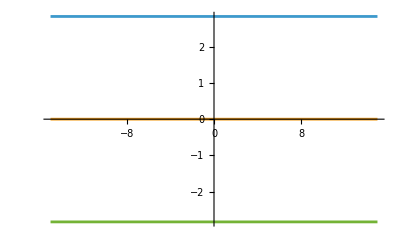

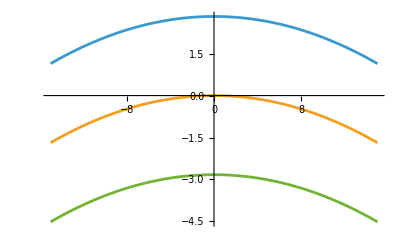

```mathematica
Plot[{ωAS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωS[μ]-ωC[μ]}, {μ,-15,15}]
Plot[{ωAS[μ]-d1×μ,ωC[μ]-d1×μ,ωS[μ]-d1×μ}, {μ,-15,15}]
```

```mathematica
(*plt1=Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt2=Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,Orange}];
plt3=Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt4=Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-50,50},FrameLabel->{"μ","(ω-ω_0) / 2π"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}];
Grid[{{plt1,plt2,plt3,plt4}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]*)
```

```mathematica
(*Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-450,250},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}]*)
```

## Overlap

```mathematica
norm[μ_]:=Sum[(Conjugate[bC[μ][[i]]]bC[μ][[i]])^2,{i,1,3}] ;
norm[μ]/.μ->0
```

0.5

```mathematica
bC[μ][[3]]/.μ->0
```

0.707107

```mathematica
f[0,-1,-1,0]:=Sum[Conjugate[bC[μ][[i]]]bS[0][[i]]*Conjugate[bS[0][[i]]]bC[μ][[i]] ,{i,1,3}]/norm[μ]
f[0,1,1,0]:=Sum[Conjugate[bC[μ][[i]]]bAS[0][[i]]*Conjugate[bAS[0][[i]]]bC[μ][[i]] ,{i,1,3}]/norm[μ]
f[0,-1,0,1]:=Sum[Conjugate[bC[μ][[i]]]bS[0][[i]]*Conjugate[bAS[0][[i]]]bC[μ][[i]] ,{i,1,3}]/norm[μ]
```

```mathematica
f[-1,-1,-1,-1]:=Sum[Conjugate[bS[μ][[i]]]bS[0][[i]]*Conjugate[bS[0][[i]]]bC[μ][[i]] ,{i,1,3}]/norm[μ]
f[-1,1,1,-1]:=Sum[Conjugate[bS[μ][[i]]]bAS[0][[i]]*Conjugate[bS[0][[i]]]bAS[μ][[i]] ,{i,1,3}]/norm[μ]
```

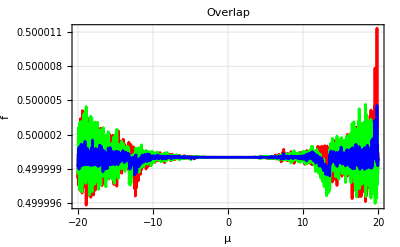

```mathematica
Plot[{f[0,-1,-1,0],f[0,1,1,0],f[0,-1,0,1]},{μ,-20,20},FrameLabel->{"μ","f"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}]
```

```mathematica
muVals=Range[-20,20,.1];
data=Table[{μ,f[0,-1,0,1]},{μ,muVals}];
dataWithHeader=Prepend[data,{"mu","f_DOPO"}];
Export["/home/eduardo/Documents/Ciencia/UNICAMP/[Proj]onChipOPO/Calculations_new/r-2r-r-molecule/notebooks/Data/DOPO overlap symmetric.csv",dataWithHeader]
```

/home/eduardo/Documents/Ciencia/UNICAMP/[Proj]onChipOPO/Calculations_new/r-2r-r-molecule/notebooks/Data/DOPO overlap symmetric.csv

```mathematica
g:=gain/.{ ap[τ]^2 Conjugate[ap[τ]]^2->P^2};
gpump:=gainpump/.{ κp->.2, κ[0]->.2};
```

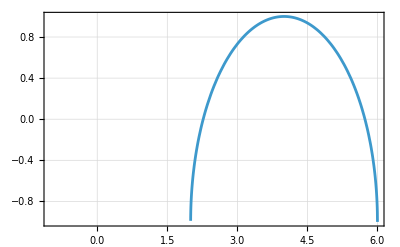

```mathematica
Plot[g/.{μ->0}/.{P->2} ,{Δ,-1,6},PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14]]
```

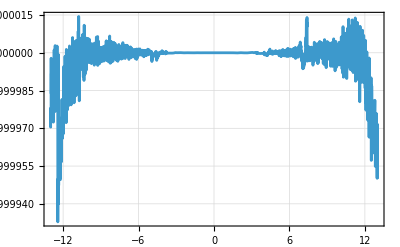

```mathematica
Plot[Re[g]/.{Δ->4, P->2} ,{μ,-13,13},PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14]]
```

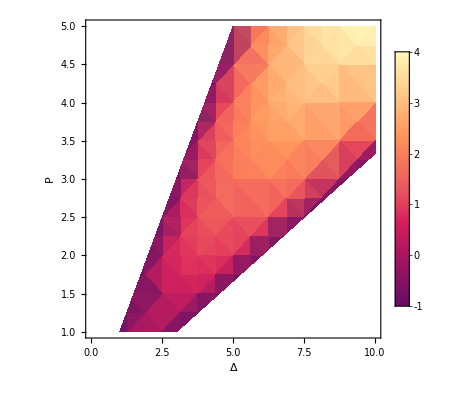

```mathematica
DensityPlot[g/.{μ->0},{Δ,0,10},{P,1,5}, PlotPoints->5, FrameLabel->{"Δ","P"},PlotTheme->"Detailed"]
```

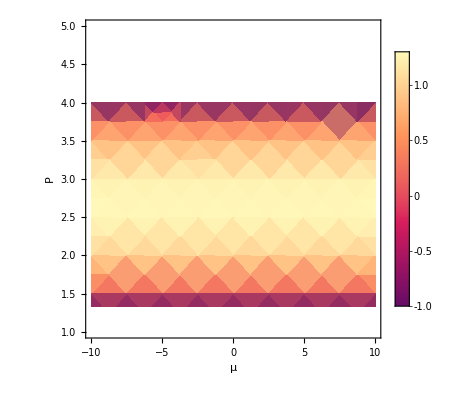

```mathematica
DensityPlot[g/.{Δ->4},{μ,-10,10},{P,1,5}, PlotPoints->5, FrameLabel->{"μ","P"},PlotTheme->"Detailed"]
```

```mathematica
Plot[Re[g]/.{Δ->2*2, P->2} ,{μ,-13,13},PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14]]
```

$Aborted

Export

```mathematica
muVals=Range[-20,20,.5];
```

```mathematica
data=Table[{μ,g/.{Δ->4, P->2}},{μ,muVals}];
```

```mathematica
dataWithHeader=Prepend[data,{"mu","g"}];
```

```mathematica
Export["/home/eduardo/Documents/Ciencia/UNICAMP/[Proj]onChipOPO/Calculations_new/r-2r-r-molecule/notebooks/Data/gain.csv",dataWithHeader]
```

/home/eduardo/Documents/Ciencia/UNICAMP/[Proj]onChipOPO/Calculations_new/r-2r-r-molecule/notebooks/Data/gain.csv

```mathematica
g/.{Δ->0, P->2}
```

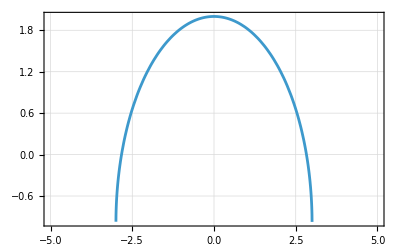

```mathematica
Plot[gpump/.{μ->0}/.{P->2} ,{Δp,-5,5},PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14]]
```

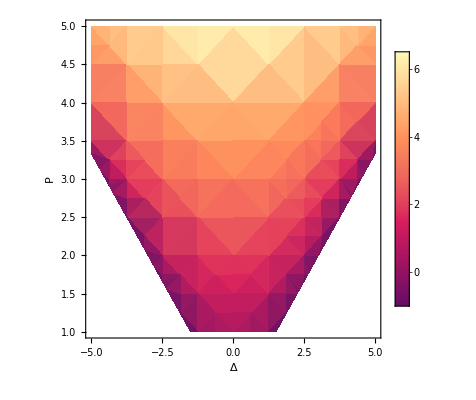

```mathematica
DensityPlot[gpump/.{μ->0},{Δp,-5,5},{P,1,5}, PlotPoints->5, FrameLabel->{"Δ","P"},PlotTheme->"Detailed"]
```